### before rotating back

```mathematica
Quit[]
```

```mathematica
rot [mat_]:= Block[{R},
   R={{nx/(√(1-nz^2)),-ny/(√(1-nz^2)),0},{ny/(√(1-nz^2)),nx/(√(1-nz^2)),0},{0,0,1}};   
   R.(mat/.{nx->Sqrt[1-nz nz]}).Transpose[R]//Simplify[#,nx nx+ny ny +nz nz ==1]&]
mat = ({{0, -(2 (ϵ-nz Δ)^2 (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6), 0}, {-(2 (ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)) λ)/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4), 0, 0}, {0, (2 nx Δ (nz Δ-ϵ) (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6), 0}})
mat=mat+(mat/.{nx->-nx,ny->-ny,nz->-nz});
mat=mat/.ny->0//Simplify[#,nx nx+nz nz==1]&
```

(0 | -(2 (ϵ-nz Δ)^2 (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6) | 0
-(2 (ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)) λ)/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4) | 0 | 0
0 | (2 nx Δ (nz Δ-ϵ) (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6) | 0)

(0 | (2 (nz Δ+ϵ)^2 (ϵ^3+3 Δ^2 ϵ+nz (Δ^3+3 ϵ^2 Δ)) λ)/(3 (nz^2+2) Δ^6+18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4-4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2+2 nz ϵ^5 Δ+ϵ^6)-(2 (ϵ-nz Δ)^2 (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6) | 0
-(4 ϵ (3 Δ^2+ϵ^2) λ)/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4) | 0 | 0
0 | 2 nx Δ λ (((nz Δ-ϵ) (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)))/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6)-((nz Δ+ϵ) (ϵ^3+3 Δ^2 ϵ+nz (Δ^3+3 ϵ^2 Δ)))/(3 (nz^2+2) Δ^6+18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4-4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2+2 nz ϵ^5 Δ+ϵ^6)) | 0)

```mathematica
σxx=(2 (-3 Δ^4+2 (ϵ^2+4 nz^2 λ^2) Δ^2+ϵ^4))/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4);
σyy=(2 (-3 (nz^2+2)^2 Δ^12-2 ((8 nz^4-37 nz^2+2) ϵ^2-20 nz^2 (nz^2+2) λ^2) Δ^10-((14 nz^4-8 nz^2+3) ϵ^4+16 (4 nz^4+13 nz^2-3) λ^2 ϵ^2+128 nz^4 λ^4) Δ^8+4 ϵ^2 ((6 nz^4-15 nz^2+2) ϵ^4+2 (17 nz^4-12 nz^2+5) λ^2 ϵ^2+32 nz^2 (nz^4+1) λ^4) Δ^6+ϵ^4 (3 (3 nz^4-4 nz^2+2) ϵ^4+16 (nz^4-nz^2+2) λ^2 ϵ^2-128 nz^4 λ^4) Δ^4+2 ϵ^8 ((nz^2+2) ϵ^2+4 (1-2 nz^2) λ^2) Δ^2+ϵ^12))/((3 (nz^2+2) Δ^6+18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4-4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2+2 nz ϵ^5 Δ+ϵ^6) (3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6));
```

```mathematica
Clear[a1,a2,a3]
z={0,0,1};
Evec = {Ex,Ey,0};
j = {Hold[σxx] Ex,Hold[σyy] Ey,0};
npara = {nx,0,0};
nperp = {0,0,nz};
({{0, a1, 0}, {a2, 0, 0}, {0, a3, 0}}).Evec
sol=Solve[%==a z×j + b npara×(npara × (z×j))+c npara×(nperp×(z×j)),{a,b,c}]//Simplify
a1 = mat[[1,2]];a2=mat[[2,1]];a3=mat[[3,2]];

ap=a/.sol//Limit[#,nz->0]&//Simplify//Factor
bp=b/.sol//Limit[#,nz->0]&//Limit[#,nx->1]&//Simplify//Factor
cp=c/.sol//Limit[#,nz->0]&//Simplify//Factor
```

{a1 Ey,a2 Ex,a3 Ey}

{{a→-a1/Hold[σyy],b→-(a1 Hold[σxx]+a2 Hold[σyy])/(nx^2 Hold[σxx] Hold[σyy]),c→-a3/(nx nz Hold[σyy])}}

{-(4 λ ϵ^3)/((2 Δ^4+Δ^2 ϵ^2+ϵ^4) Hold[σyy])}

{-(4 λ ϵ (-2 Δ^4 Hold[σyy]+3 Δ^2 ϵ^2 Hold[σxx]-Δ^2 ϵ^2 Hold[σyy]+ϵ^4 Hold[σxx]-ϵ^4 Hold[σyy]))/((3 Δ^2+ϵ^2) (2 Δ^4+Δ^2 ϵ^2+ϵ^4) Hold[σxx] Hold[σyy])}

{(8 Δ^2 λ ϵ (4 Δ^6-3 Δ^4 ϵ^2-2 Δ^2 ϵ^4+8 Δ^2 λ^2 ϵ^2+ϵ^6))/((3 Δ^2+ϵ^2) (2 Δ^4+Δ^2 ϵ^2+ϵ^4)^2 Hold[σyy])}

```mathematica
a0=λ/ϵ;
ap/a0/.nz->0/.Δ->ϵ δ/.λ->Λ ϵ/2//Simplify//Factor;
%//ReleaseHold//ReplaceAll[#,{nz->0,Δ->ϵ δ,λ->Λ ϵ/2}]&//Simplify//Factor
bp/(2ap δ^2)/.nz->0/.Δ->ϵ δ/.λ->Λ ϵ/2//Simplify;
%//ReleaseHold//ReplaceAll[#,{nz->0,Δ->ϵ δ,λ->Λ ϵ/2}]&//Simplify
cp/(-2ap δ^2)/.nz->0/.Δ->ϵ δ/.λ->Λ ϵ/2//Simplify//Together;
%//ReleaseHold//ReplaceAll[#,{nz->0,Δ->ϵ δ,λ->Λ ϵ/2}]&//Simplify
```

{(2 (3 δ^2+1))/(2 δ^6-δ^4-2 δ^2 Λ^2-1)}

{(δ^4-2 δ^2-Λ^2+1)/(-3 δ^4+2 δ^2+1)}

{(4 δ^6-3 δ^4+2 δ^2 (Λ^2-1)+1)/(6 δ^6+5 δ^4+4 δ^2+1)}

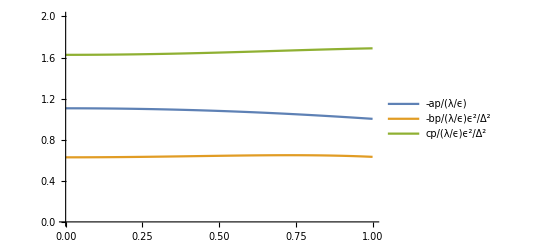

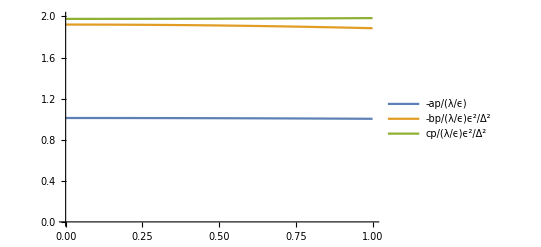

```mathematica
ap=ReleaseHold[a/.sol]//Simplify[#,nx nx+nz nz==1]&;
bp=ReleaseHold[b/.sol]//Simplify//Simplify[#,nx nx+nz nz==1]&//Simplify//ReplaceAll[#,nx^-2->1/(1-nz^2)]&;
cp=ReleaseHold[c/.sol]//Simplify//Simplify[#,nx nx+nz nz==1]&;
nsub = {ϵ->4,λ->1.5,Δ->1};
Plot[Evaluate[1/2{-ap/(λ/ϵ),-bp/(λ/ϵ)ϵ^2/Δ^2,cp/(λ/ϵ)ϵ^2/Δ^2}/.nsub],{nz,0,1},PlotLegends->{"-ap/(λ/ϵ)","-bp/(λ/ϵ)ϵ^2/Δ^2","cp/(λ/ϵ)ϵ^2/Δ^2"},PlotRange->{0,2}]

nsub = {ϵ->16,λ->1.5,Δ->1};
Plot[Evaluate[1/2{-ap/(λ/ϵ),-bp/(λ/ϵ)ϵ^2/Δ^2,cp/(λ/ϵ)ϵ^2/Δ^2}/.nsub],{nz,0,1},PlotLegends->{"-ap/(λ/ϵ)","-bp/(λ/ϵ)ϵ^2/Δ^2","cp/(λ/ϵ)ϵ^2/Δ^2"},PlotRange->{0,2}]
```

### after rotating back

```mathematica
Quit[]
```

```mathematica
rot [mat_]:= Block[{R},
   R={{nx/(√(1-nz^2)),-ny/(√(1-nz^2)),0},{ny/(√(1-nz^2)),nx/(√(1-nz^2)),0},{0,0,1}};   
   R.(mat/.{nx->Sqrt[1-nz nz]}).Transpose[R]//Simplify[#,nx nx+ny ny +nz nz ==1]&]

mat = ({{0, -(2 (ϵ-nz Δ)^2 (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6), 0}, {-(2 (ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)) λ)/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4), 0, 0}, {0, (2 nx Δ (nz Δ-ϵ) (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6), 0}})//rot
mat=mat+(mat/.{nx->-nx,ny->-ny,nz->-nz});
mat=%//Simplify[#,nx nx+ny ny+nz nz==1]&
```

((4 nx ny Δ^2 (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ (-3 Δ^4+2 (ϵ^2+4 nz^2 λ^2) Δ^2-8 nz ϵ λ^2 Δ+ϵ^4))/((9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4) (3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6)) | (2 λ ((ny^2 (ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)))/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4)-(nx^2 (ϵ-nz Δ)^2 (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)))/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6)))/(1-nz^2) | 0
(2 λ ((ny^2 (ϵ-nz Δ)^2 (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)))/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6)-(nx^2 (ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)))/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4)))/(1-nz^2) | (4 nx ny Δ^2 (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ (3 Δ^4-2 (ϵ^2+4 nz^2 λ^2) Δ^2+8 nz ϵ λ^2 Δ-ϵ^4))/((9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4) (3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6)) | 0
-(2 ny Δ (nz Δ-ϵ) (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6) | (2 nx Δ (nz Δ-ϵ) (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6) | 0)

((4 nx ny Δ^2 λ (((nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) (-3 Δ^4+2 (ϵ^2+4 nz^2 λ^2) Δ^2-8 nz ϵ λ^2 Δ+ϵ^4))/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6)-((ϵ^3+3 Δ^2 ϵ+nz (Δ^3+3 ϵ^2 Δ)) (-3 Δ^4+2 (ϵ^2+4 nz^2 λ^2) Δ^2+8 nz ϵ λ^2 Δ+ϵ^4))/(3 (nz^2+2) Δ^6+18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4-4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2+2 nz ϵ^5 Δ+ϵ^6)))/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4) | (2 λ (((ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)) ny^2)/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4)+((ϵ^3+3 Δ^2 ϵ+nz (Δ^3+3 ϵ^2 Δ)) ny^2)/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4)-(nx^2 (nz Δ+ϵ)^2 (-ϵ (3 Δ^2+ϵ^2)-nz (Δ^3+3 ϵ^2 Δ)))/(3 (nz^2+2) Δ^6+18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4-4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2+2 nz ϵ^5 Δ+ϵ^6)-(nx^2 (ϵ-nz Δ)^2 (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)))/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6)))/(1-nz^2) | 0
(2 λ (-((ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)) nx^2)/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4)-((ϵ^3+3 Δ^2 ϵ+nz (Δ^3+3 ϵ^2 Δ)) nx^2)/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4)+(ny^2 (nz Δ+ϵ)^2 (-ϵ (3 Δ^2+ϵ^2)-nz (Δ^3+3 ϵ^2 Δ)))/(3 (nz^2+2) Δ^6+18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4-4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2+2 nz ϵ^5 Δ+ϵ^6)+(ny^2 (ϵ-nz Δ)^2 (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)))/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6)))/(1-nz^2) | (4 nx ny Δ^2 λ (((ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)) (-3 Δ^4+2 (ϵ^2+4 nz^2 λ^2) Δ^2-8 nz ϵ λ^2 Δ+ϵ^4))/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6)+((ϵ^3+3 Δ^2 ϵ+nz (Δ^3+3 ϵ^2 Δ)) (-3 Δ^4+2 (ϵ^2+4 nz^2 λ^2) Δ^2+8 nz ϵ λ^2 Δ+ϵ^4))/(3 (nz^2+2) Δ^6+18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4-4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2+2 nz ϵ^5 Δ+ϵ^6)))/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4) | 0
2 ny Δ λ (((-nz Δ-ϵ) (-ϵ (3 Δ^2+ϵ^2)-nz (Δ^3+3 ϵ^2 Δ)))/(3 (nz^2+2) Δ^6+18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4-4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2+2 nz ϵ^5 Δ+ϵ^6)-((nz Δ-ϵ) (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)))/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6)) | 2 nx Δ λ (((nz Δ-ϵ) (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)))/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6)-((nz Δ+ϵ) (ϵ^3+3 Δ^2 ϵ+nz (Δ^3+3 ϵ^2 Δ)))/(3 (nz^2+2) Δ^6+18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4-4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2+2 nz ϵ^5 Δ+ϵ^6)) | 0)

```mathematica
σxx=(2 (-3 Δ^4+2 (ϵ^2+4 nz^2 λ^2) Δ^2+ϵ^4))/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4);
σyy=(2 (-3 (nz^2+2)^2 Δ^12-2 ((8 nz^4-37 nz^2+2) ϵ^2-20 nz^2 (nz^2+2) λ^2) Δ^10-((14 nz^4-8 nz^2+3) ϵ^4+16 (4 nz^4+13 nz^2-3) λ^2 ϵ^2+128 nz^4 λ^4) Δ^8+4 ϵ^2 ((6 nz^4-15 nz^2+2) ϵ^4+2 (17 nz^4-12 nz^2+5) λ^2 ϵ^2+32 nz^2 (nz^4+1) λ^4) Δ^6+ϵ^4 (3 (3 nz^4-4 nz^2+2) ϵ^4+16 (nz^4-nz^2+2) λ^2 ϵ^2-128 nz^4 λ^4) Δ^4+2 ϵ^8 ((nz^2+2) ϵ^2+4 (1-2 nz^2) λ^2) Δ^2+ϵ^12))/((3 (nz^2+2) Δ^6+18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4-4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2+2 nz ϵ^5 Δ+ϵ^6) (3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6));
```

```mathematica
Clear[a1,a2,a3]
Clear[a11,a12,a21,a21,a22,a31,a32]

z={0,0,1};
Evec = {Ex,Ey,0};
j = {Hold[σxx] Ex,Hold[σyy] Ey,0};

npara = {nx,ny,0};
nperp = {0,0,nz};
({{a11, a12, 0}, {a21, a22, 0}, {a31, a32, 0}}).Evec
sol=Solve[%==a z×j + b npara×(npara × (z×j))+c npara×(nperp×(z×j)),{a,b,c}]//Simplify
a11 = mat[[1,1]];a12=mat[[1,2]];
a21 = mat[[2,1]];a22=mat[[2,2]];
a31 = mat[[3,1]];a32=mat[[3,2]];

ap=a/.sol//Limit[#,nz->0]&//Limit[#,nx->1]&//Limit[#,ny->0]&
bp=b/.sol//Limit[#,nz->0]&//Limit[#,nx->1]&//Limit[#,ny->0]&
cp=c/.sol//Limit[#,nz->0]&//Limit[#,nx->1]&//Limit[#,ny->0]&
```

{a11 Ex+a12 Ey,a21 Ex+a22 Ey,a31 Ex+a32 Ey}

{{a→(a11 Ex nx+a12 Ey nx+a21 Ex ny+a22 Ey ny)/(Ex ny Hold[σxx]-Ey nx Hold[σyy]),b→(Ex Hold[σxx] (a11 Ex+a12 Ey)+Ey Hold[σyy] (a21 Ex+a22 Ey))/((Ex ny Hold[σxx]-Ey nx Hold[σyy]) (Ex nx Hold[σxx]+Ey ny Hold[σyy])),c→(a31 Ex+a32 Ey)/(Ex ny nz Hold[σxx]-Ey nx nz Hold[σyy])}}

{-(4 λ ϵ^3 (3 Δ^2+ϵ^2))/((6 Δ^6+5 Δ^4 ϵ^2+4 Δ^2 ϵ^4+ϵ^6) Hold[σyy])}

{-((4 Ex Ey λ ϵ^3 (3 Δ^2+ϵ^2) Hold[σxx])/(6 Δ^6+5 Δ^4 ϵ^2+4 Δ^2 ϵ^4+ϵ^6)-(4 Ex Ey λ (3 Δ^2 ϵ+ϵ^3) Hold[σyy])/(9 Δ^4+6 Δ^2 ϵ^2+ϵ^4))/(Ex Ey Hold[σxx] Hold[σyy])}

{(8 Δ^2 λ ϵ (4 Δ^6-3 Δ^4 ϵ^2-2 Δ^2 (ϵ^4-4 λ^2 ϵ^2)+ϵ^6))/((3 Δ^2+ϵ^2) (2 Δ^4+Δ^2 ϵ^2+ϵ^4)^2 Hold[σyy])}

```mathematica
a0=λ/ϵ;
ap/a0/.nz->0/.Δ->ϵ δ/.λ->Λ ϵ/2//Simplify//Factor;
%//ReleaseHold//ReplaceAll[#,{nz->0,Δ->ϵ δ,λ->Λ ϵ/2}]&//Simplify//Factor
bp/(2ap δ^2)/.nz->0/.Δ->ϵ δ/.λ->Λ ϵ/2//Simplify;
%//ReleaseHold//ReplaceAll[#,{nz->0,Δ->ϵ δ,λ->Λ ϵ/2}]&//Simplify
cp/(-2ap δ^2)/.nz->0/.Δ->ϵ δ/.λ->Λ ϵ/2//Simplify//Together;
%//ReleaseHold//ReplaceAll[#,{nz->0,Δ->ϵ δ,λ->Λ ϵ/2}]&//Simplify
```

{(2 (3 δ^2+1))/(2 δ^6-δ^4-2 δ^2 Λ^2-1)}

{(δ^4-2 δ^2-Λ^2+1)/(-3 δ^4+2 δ^2+1)}

{(4 δ^6-3 δ^4+2 δ^2 (Λ^2-1)+1)/(6 δ^6+5 δ^4+4 δ^2+1)}

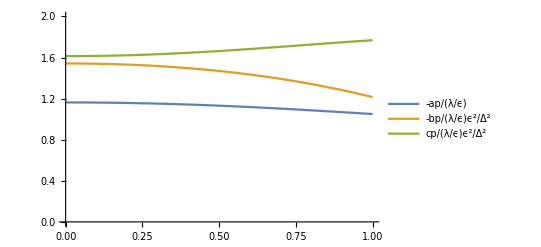

-Graphics-

```mathematica
ap=ReleaseHold[a/.sol]//ReplaceAll[#,{ny->0,nx->Sqrt[1-nz nz]}]&;
bp=ReleaseHold[b/.sol]//ReplaceAll[#,{ny->0,nx->Sqrt[1-nz nz]}]&;
cp=ReleaseHold[c/.sol]//ReplaceAll[#,{ny->0,nx->Sqrt[1-nz nz]}]&;
nsub = {ϵ->4,λ->0.75,Δ->1};
Plot[Evaluate[1/2{-ap/(λ/ϵ),-bp/(λ/ϵ)ϵ^2/Δ^2,cp/(λ/ϵ)ϵ^2/Δ^2}/.nsub],{nz,0,1},PlotLegends->{"-ap/(λ/ϵ)","-bp/(λ/ϵ)ϵ^2/Δ^2","cp/(λ/ϵ)ϵ^2/Δ^2"},PlotRange->{0,2}]

nsub = {ϵ->16,λ->1.5,Δ->1};
Plot[Evaluate[1/2{-ap/(λ/ϵ),-bp/(λ/ϵ)ϵ^2/Δ^2,cp/(λ/ϵ)ϵ^2/Δ^2}/.nsub],{nz,0,1},PlotLegends->{"-ap/(λ/ϵ)","-bp/(λ/ϵ)ϵ^2/Δ^2","cp/(λ/ϵ)ϵ^2/Δ^2"},PlotRange->{0,2}]
```

```mathematica
-ap/(λ/ϵ)/.nsub/.nz->0.5
```

{2.69188 nx^2}